# Assignment 7

## Problem 1

77

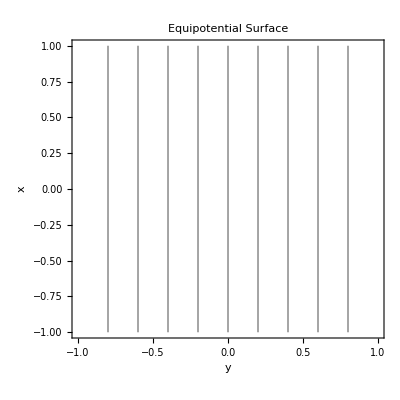

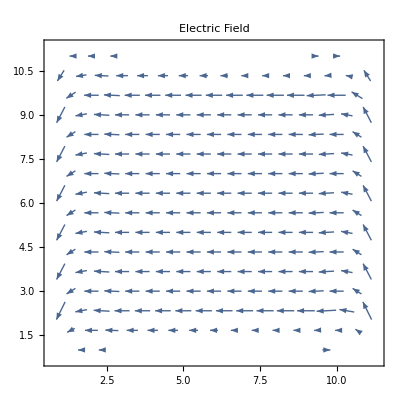

-Graphics3D-

```mathematica
dx = 0.2;
xL = Range[-1,1,dx];
lx=Length[Range[-1,1,dx]];
v = Table[0,{i,lx},{j,lx}];
v[[1]]=xL;
v[[lx]] = xL;
v[[All,1]]=-1;
v[[All,-1]]=1;
tol = 0.00001;
cond = 0;
vo = v;
counter=0;
While[cond==0,
 Do[
Do[v[[i,j]]=0.25(v[[i+1,j]]+v[[i-1,j]]+v[[i,j+1]]+v[[i,j-1]]),{i,2,lx-1}]
,{j,2,lx-1}];
dv = Abs[v-vo];
If[Max[dv]< tol,cond = 1]; vo = v;counter++];
counter

l=v//MatrixForm;
ListContourPlot[v,Axes->True,AxesLabel-> {y,x},PlotLabel->"Equipotential Surface", DataRange->{{-1,1},{-1,1}},PlotLegends->None, ContourShading->None, AspectRatio->Automatic]

efi = v;efj=v; 
Do[
efi[[j,1]]= - (v[[j,2]] -v[[j,1]])/(2dx);
efi[[j,lx]]= +(v[[j,lx-1]] - v[[j,lx]])/(2dx);
efj[[1,j]]= - (v[[2,j]] -v[[1,j]])/(2dx); 
efj[[lx,j]]= + (v[[lx-1,j]] - v[[lx,j]])/(2dx),{j,1,lx}];


Do[Do[efi[[j,i]] =-(v[[j,i+1]]-v[[j,i-1]])/(2.0  dx);efj[[i,j]]=-((v[[i-1,j]]-v[[i+1,j]])/(2.0 dx)), {i,2,lx-1}] ,{j,2,lx-1}]; 
ef=Transpose@{Flatten[efi],Flatten[efj]};
ef=Transpose[Partition[ef,lx]];
p1p =ListVectorPlot[ef,PlotLegends->Automatic,PlotLabel->"Electric Field", VectorScaling->"Linear", VectorSizes->{0,1}, VectorColorFunction->None]
ListPlot3D[v]
```

## Problem 2:

Fig 5.5

{1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1,0.,-0.1,-0.2,-0.3,-0.4,-0.5,-0.6,-0.7,-0.8,-0.9,-1.}

{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

331

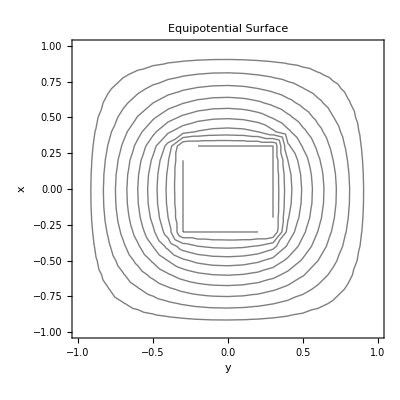

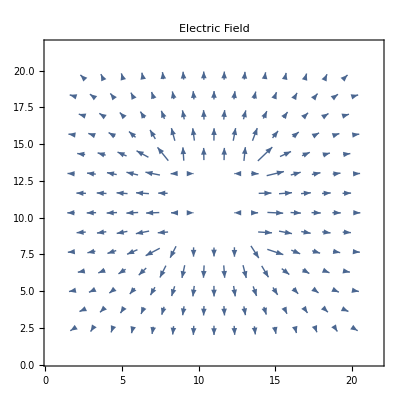

-Graphics3D-

```mathematica
ClearAll[v2,vo2]
ddx = 0.1;
xxL = Range[1,-1,-ddx];
xxL
llx=Length[xxL];
yyL = Union[Range[-1,-.3,ddx],Range[.3,1,ddx]];
lly=Length[yyL];
v2 = Table[0,{i,llx},{j,llx}];
v2[[1]]=xxL;
v2[[llx]] = xxL;
v2[[1;;-1,1;;-1]]=0;
v2[[8;;14,8;;14]]=1;
tol = 0.0000000000001;
cond = 0;
vo2 = v2;
ccounter = 0;
l1=Union[xxL[[1;;8]],xxL[[-8;;-1]]]
k1=xxL[[8;;-8]];
While[cond==0,
 Do[
Do[v2[[i,j]]=0.25(v2[[i+1,j]]+v2[[i-1,j]]+v2[[i,j+1]]+v2[[i,j-1]]),{i,2,20}]
,{j,2,llx-1}];
v2[[8;;14,8;;14]]=1;
ddv = Abs[v2-vo2];
If[Max[ddv]< tol,cond = 1]; vo2 = v2;ccounter++];
ccounter

l2=v2//MatrixForm;
ListContourPlot[v2,Axes->True,AxesLabel-> {y,x},PlotLabel->"Equipotential Surface", DataRange->{{-1,1},{-1,1}},PlotLegends->None, ContourShading->None, AspectRatio->Automatic]

eefi = v2;eefj=v2; 

Do[Do[eefi[[j,i]] =(-(v2[[i+1,j]]-v2[[i-1,j]])/2.0  ddx 3);eefj[[i,j]]=-((v2[[j,i+1]]-v2[[j,i-1]])/2.0 ddx 3), {i,2,llx-1}] ,{j,1,llx}]; 
eef=Partition[{Flatten[eefi],Flatten[eefj]},llx];
eef=Transpose[Partition[eef,llx]];
p2p =ListVectorPlot[eef,PlotLegends->Automatic,PlotLabel->"Electric Field", VectorScaling->"Linear",PlotRange->{{-1,1},{-1,1}}, VectorSizes->{0,1}, VectorColorFunction->None]
ListPlot3D[v2]
```

## Problem 3

Fig 5.7

362

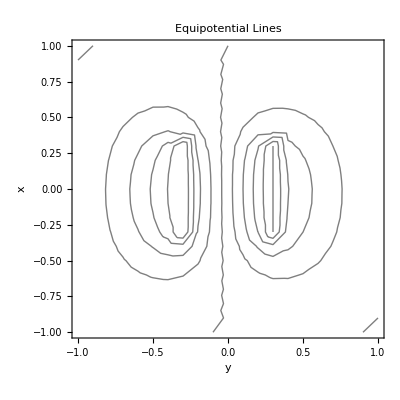

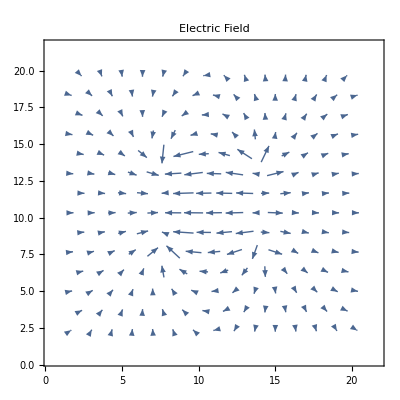

-Graphics3D-

```mathematica
ClearAll["Global `*"]
ddx = 0.1;
xL3 = Range[1,-1,-ddx];
lx3=Length[xL3];
yl3=Range[1,-1,ddx];
ly3=Length[yl3];
vv3 = Table[0,{i,lx3},{j,lx3}];
vv3[[1]]=xL3;
vv3[[lx3]] = xL3;
vv3[[1;;-1,1;;-1]]=0;
tol = 0.0000000000001;
cond = 0;
vv3o = vv3;
cccounter = 0;
While[cond==0, Do[
Do[vv3[[i,j]]=0.25(vv3[[i+1,j]]+vv3[[i-1,j]]+vv3[[i,j+1]]+vv3[[i,j-1]]),{j,2,lx3-1}]
,{i,2,lx3-1}]; 
vv3[[8;;-8,8]]=-1;vv3[[8;;-8,14]]=1;
ddv3 = Abs[vv3-vv3o];
If[Max[ddv3]< tol,cond = 1]; vv3o = vv3;cccounter++];
cccounter
ll3=vv3//MatrixForm;
ListContourPlot[vv3,Axes->True,AxesLabel-> {y,x},PlotLabel->"Equipotential Lines", DataRange->{{-1,1},{-1,1}},PlotLegends->None, ContourShading->None]

eeefi = vv3;eeefj=vv3; 

Do[Do[eeefj[[i,j]] =(-(vv3[[i+1,j]]-vv3[[i-1,j]])/2.0  ddx 3);eeefi[[j,i]]=-((vv3[[j,i+1]]-vv3[[j,i-1]])/2.0 ddx 3), {i,2,lx3-1}] ,{j,1,lx3}]; 
eeef=Transpose@{Flatten[eeefi],Flatten[eeefj]};
eeef=Transpose[Partition[eeef,lx3]];
p2p3 =ListVectorPlot[eeef,PlotLegends->Automatic,PlotLabel->"Electric Field", VectorScaling->"Linear", VectorSizes->{0,1}, VectorColorFunction->None]
ListPlot3D[vv3]
```

## Problem 4

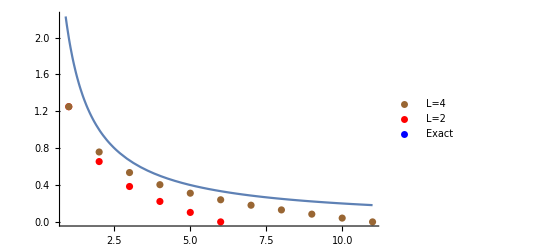

```mathematica
Clear["Global`*"];
(*for x=4*)

L=4;
step=0.2;
x4=Range[-L/2,L/2,step]/L;
len=Length[x4];
ρ=step^(-3);
NewV= V= Table[0,len,len];
m= Round[len/2] +1;
n=0;
dV=1;
While[ n<1000,
	For[i=2,i<len,i++, 
		For[j=2, j<len,j++,
			NewV[[i,j]]= (V[[i-1,j]]+V[[i+1,j]] +V[[i,j+1]] + V[[i,j-1]])/4;
		]
	];
	NewV[[m,m]] =+ (ρ*step^2)/4;
	For[i=2,i<len,i++, 
		For[j=2, j<len,j++,
			V[[i,j]]= (NewV[[i-1,j]]+NewV[[i+1,j]] +NewV[[i,j+1]] + NewV[[i,j-1]])/4;
		]
	];
	V[[m,m]] =+ (ρ*step^2)/4;
	diff= Abs[V-NewV];
	dV = Total[Flatten[diff]];
	n=n+2;
]

voltageLis4= V[[m,m;;]];

(*for x=2*)
L=2;
step=0.2;
x2=Range[-L/2,L/2,step]/L;
len=Length[x2];
ρ=step^(-3);
NewV= V= Table[0,len,len];
m= Round[len/2];
n=0;
dV=1;
While[ n<3000,
	For[i=2,i<len,i++, 
		For[j=2, j<len,j++,
			NewV[[i,j]]= (V[[i-1,j]]+V[[i+1,j]] +V[[i,j+1]] + V[[i,j-1]])/4;
		]
	];
	NewV[[m,m]] =+ (ρ*step^2)/4;
	For[i=2,i<len,i++, 
		For[j=2, j<len,j++,
			V[[i,j]]= (NewV[[i-1,j]]+NewV[[i+1,j]] +NewV[[i,j+1]] + NewV[[i,j-1]])/4;
		]
	];
	V[[m,m]] =+ (ρ*step^2)/4;
	diff= Abs[V-NewV];
	dV = Total[Flatten[diff]];
	n=n+2;
]

voltageLis2= V[[m,m;;]];

a=ListPlot[{voltageLis2}, PlotStyle->Red];
b=ListPlot[voltageLis4, PlotStyle->Brown];
c= Plot[ {2/(x)}, {x, 0, 11}];
graph=Show[a, b,c, PlotRange->Automatic, PlotLegends->PointLegend[Automatic]];
Legended[graph, PointLegend[{Brown, Red, Blue}, {"L=4", "L=2","Exact"}]]
```